```mathematica
f[x_]:=0 /; x≤1
f[x_]:=x^2/2-x+1/2/;1<x≤4
f[x_]:=-x^2/2+7*x-31/2/;4<x≤10
f[x_]:=x^2/2-13*x+169/2/;10<x≤13
f[x_]:=0/;x>13
```

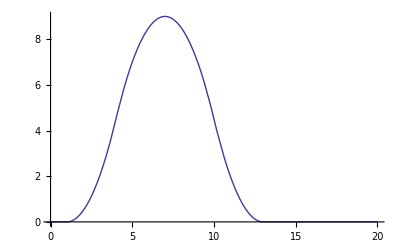

```mathematica
Plot[f[x],{x,0,20}]
```

```mathematica
Integrate[Exp[-i*x*r-g^2*r^2],r]
```

(ⅇ^((i^2 x^2)/(4 g^2)) √π Erf[g r+(i x)/(2 g)])/(2 g)

```mathematica
Erf[-Infinity]
```

-1

```mathematica
Erf[Infinity]
```

1

```mathematica
Erf[i]
```

```mathematica
Erf[i]
```

Erf[i]

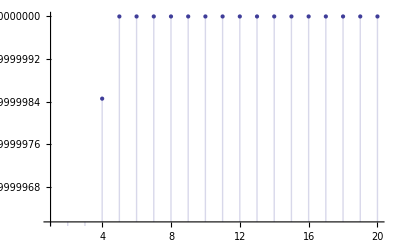

```mathematica
DiscretePlot[Erf[i],{i,1,20}]
```

```mathematica
i+2i
```

```mathematica
Erf[2]
```

Erf[2]

```mathematica
N[Erf[2]]
```

0.995322

```mathematica
-Infinity+i
```

-∞

```mathematica
Integrate[Exp[-I*w*x]*(x^2/2-x+1/2),{x,1,4}]
```

(ⅇ^(-4 ⅈ w) (-2 ⅈ+2 ⅈ ⅇ^(3 ⅈ w)+6 w+9 ⅈ w^2))/(2 w^3)

(ⅇ^(-4 i w) (-2+2 ⅇ^(3 i w)-3 i w (2+3 i w)))/(2 i^3 w^3)

```mathematica
Abs[1+2I]
```

√5

```mathematica
Abs[Integrate[Exp[-I*w*x]*(x^2/2-x+1/2),{x,1,4}]]
```

1/2 ⅇ^(4 Im[w]) Abs[(-2 ⅈ+2 ⅈ ⅇ^(3 ⅈ w)+6 w+9 ⅈ w^2)/w^3]

```mathematica
Abs[(-2 ⅈ-2Sin[3w]+I*Cos[3w]+6 w+9 ⅈ w^2)/w^3]
```

Abs[(-2 ⅈ+6 w+9 ⅈ w^2+ⅈ Cos[3 w]-2 Sin[3 w])/w^3]

```mathematica
f[w]:=1/(4*w^6)*Exp[w^2/4]*((6w-2Sin[3w])^2+(Cos[3w]+9*w^2-2)^2)
```

```mathematica
f[1]
```

0

```mathematica
f[2]
```

1/2

```mathematica
f[3]
```

2

```mathematica
f[4]
```

9/2

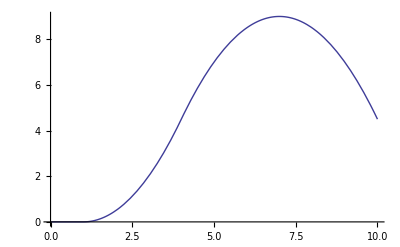

```mathematica
Plot[f[x],{x,0,10}]
```

```mathematica
f[.5]
```

0

```mathematica
g[w_]:=1/(4*w^6)*Exp[w^2/4]*((6w-2Sin[3w])^2+(Cos[3w]+9*w^2-2)^2)
```

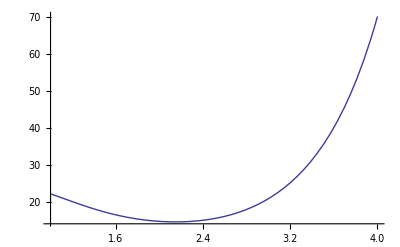

```mathematica
Plot[g[w],{w,1,4}]
```

```mathematica
Integrate[g[w],{w,1,4}]
```

∫_1^4 (ⅇ^(w^2/4) ((-2+9 w^2+Cos[3 w])^2+(6 w-2 Sin[3 w])^2))/(4 w^6)ⅆw

```mathematica
kernel[t_,x_,a_]=Exp[-a^2(x-t)^2]
```

ⅇ^(-a^2 (-t+x)^2)

```mathematica
integkukv[u_,v_,a_]=Integrate[kernel[x,u,a]kernel[x,v,a],{x,0,Pi}]
```

(ⅇ^(-1/2 a^2 (u-v)^2) √(π/2) (Erf[(a (u+v))/(√2)]-Erf[(a (-2 π+u+v))/(√2)]))/(2 a)

```mathematica
Sqrt[Integrate[(x^2/2-x+1/2)^2/Pi,{x,0,Pi}]]
```

1/2 √((1+(-1+π)^5)/(5 π))

```mathematica
N[1/2 √((1+(-1+π)^5)/(5 π))]
```

0.856091